## Обработка результатов измерений лабораторной работы №18 “Определение интегральной степени черноты твердых тел”

#### Входные данные: L-длина нити; d- ее диаметр;T2- температура жидкости(воздуха в нашем случае);σ0- константа Стефана-Больцмана; I(i)-значения силы тока на нити ; U-значения падения напряжения на нити

```mathematica
L=Quantity[280,"Millimeters"];d=Quantity[0.3,"Millimeters"];T2=Quantity[294.65,"Kelvins"];σ0=Quantity[5.67*10^-8,("Watts")/(("Meters")^2*("Kelvins")^4)];
i=Quantity[Range[1.1,2.2,0.1],"Amperes"];
U=Quantity[{0.342,0.424,0.505,0.545,0.608,0.770,0.808,0.864,0.988,1.068,1.221,1.325},"Volts"];
```

#### Площадь поверхности нити F

```mathematica
F=UnitConvert[π*d*L,("Meters")^2]
```

0.000263894 m^2

#### Электрическая мощность:

```mathematica
Q=UnitConvert[U*i,"Watts"]
```

{0.3762 W,0.5088 W,0.6565 W,0.763 W,0.912 W,1.232 W,1.3736 W,1.5552 W,1.8772 W,2.136 W,2.5641 W,2.915 W}

#### Сопротивление нити:

```mathematica
R=UnitConvert[U/i,"Ohms"]
```

{0.310909 Ω,0.353333 Ω,0.388462 Ω,0.389286 Ω,0.405333 Ω,0.48125 Ω,0.475294 Ω,0.48 Ω,0.52 Ω,0.534 Ω,0.581429 Ω,0.602273 Ω}

#### Температура нити:

```mathematica
T1=Quantity[1250*QuantityMagnitude[R] - 87,"Kelvins"]
```

{301.636 K,354.667 K,398.577 K,399.607 K,419.667 K,514.563 K,507.118 K,513. K,563. K,580.5 K,639.786 K,665.841 K}

#### Поправка П:

```mathematica
Π=7.640698*10^-5*QuantityMagnitude[T1]^2-0.1310565*QuantityMagnitude[T1]+60.67072
```

{28.0912,23.8005,20.5729,20.5007,19.1275,13.4646,13.8591,13.5467,11.1046,10.3401,8.09799,7.28253}

#### Интегральная полусферическая степень черноты:

```mathematica
ϵ=Q/(σ0*F*(T1^4-T2^4)*Π);
```

```mathematica
ϵ=ResourceFunction["DecimalRound"][{0.00834,0.010199999999999999,0.013949999999999999,0.01689,0.02259,0.02733,0.030990000000000004,0.03555,0.047099999999999996,0.050429999999999996,0.05936999999999999,0.06675},4]
```

{0.00834,0.0102,0.01395,0.01689,0.02259,0.02733,0.03099,0.03555,0.0471,0.05043,0.05937,0.06675}

#### Интегральная степень черноты ϵ в виде функции от температуры Т1:

```mathematica
ϵfromT1=Table[{QuantityMagnitude[T1[[i]]],ϵ[[i]]},{i,1,Length[T1]}]
```

{{301.636,0.00834},{354.667,0.0102},{398.577,0.01395},{399.607,0.01689},{419.667,0.02259},{514.563,0.02733},{507.118,0.03099},{513.,0.03555},{563.,0.0471},{580.5,0.05043},{639.786,0.05937},{665.841,0.06675}}

#### Стандартные значения степени черноты:

```mathematica
ϵFromT1Standard={{400,0.03},{600,0.06},{800,0.081},{1000,0.105}};
```

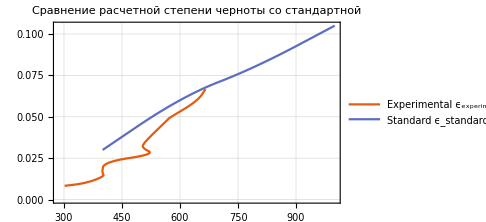

```mathematica
ListLinePlot[{ϵfromT1,ϵFromT1Standard},InterpolationOrder->Automatic,PlotLabel->"Сравнение расчетной степени черноты со стандартной",PlotTheme->"Scientific",PlotLegends->{"Experimental   ϵ_experimental(T1)","Standard   ϵ_standard(T1)"},ImageSize->Medium,GridLines->Automatic]
```